## 6/30

```mathematica
Clear@multiRule;multiRule[rules_,state_]:=<|"rule"->#,"pre"->state,"post"->CellularAutomaton[#,state]|>&/@rules
Clear@multiCA;multiCA[rules_,states_]:=Flatten[multiRule[rules,#]&/@states]
Clear@getStates;getStates[transforms_]:=#["post"]&/@transforms
Clear@evolve;evolve[rules_,initialState_,steps_]:=NestList[
	Flatten@multiCA[rules,getStates@#]&,
	Flatten@multiRule[rules,initialState],
	steps-1]
Clear@showGraph;showGraph[evo_]:=Graph[evo,
	VertexLabels->(#->Placed[ArrayPlot[{#},ImageSize->Tiny],Tooltip]&)/@Join[Values@evo,{Keys@First@evo}],
	ImageSize->Large]
Clear@getSteps;getSteps[evo_]:=(#["pre"]->#["post"])&/@Flatten@evo
Clear@getRules;getRules[evo_]:=#["rule"]&/@Flatten@evo
Clear@getVertexLabels;getVertexLabels[steps_]:=
	(#->Placed[ArrayPlot[{#},ImageSize->Tiny],Tooltip]&)/@Join[Values@steps,{Keys@First@steps}]
Clear@getEdgeLabels;getEdgeLabels[steps_,rules_]:=
	MapIndexed[#1->Tooltip[First@rules[[#2]],
		RulePlot[CellularAutomaton@First@rules[[#2]],ImageSize->Small]]&,steps]
Clear@showGraph;showGraph[evo_]:=With[{steps=getSteps@evo,rules=getRules@evo},
	Graph[steps,
	VertexLabels->getVertexLabels[steps],
	EdgeLabels->getEdgeLabels[steps,rules],
	ImageSize->Large]]
```

```mathematica
init=CenterArray[1,10];
```

```mathematica
rules={30,50};
```

```mathematica
evo=evolve[rules,init,2]
```

{{<|rule→30,pre→{0,0,0,0,1,0,0,0,0,0},post→{0,0,0,1,1,1,0,0,0,0}|>,<|rule→50,pre→{0,0,0,0,1,0,0,0,0,0},post→{0,0,0,1,0,1,0,0,0,0}|>},{<|rule→30,pre→{0,0,0,1,1,1,0,0,0,0},post→{0,0,1,1,0,0,1,0,0,0}|>,<|rule→50,pre→{0,0,0,1,1,1,0,0,0,0},post→{0,0,1,0,0,0,1,0,0,0}|>,<|rule→30,pre→{0,0,0,1,0,1,0,0,0,0},post→{0,0,1,1,0,1,1,0,0,0}|>,<|rule→50,pre→{0,0,0,1,0,1,0,0,0,0},post→{0,0,1,0,1,0,1,0,0,0}|>}}

```mathematica
getSteps@evo
```

{{0,0,0,0,1,0,0,0,0,0}→{0,0,0,1,1,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0}→{0,0,0,1,0,1,0,0,0,0},{0,0,0,1,1,1,0,0,0,0}→{0,0,1,1,0,0,1,0,0,0},{0,0,0,1,1,1,0,0,0,0}→{0,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,1,0,0,0,0}→{0,0,1,1,0,1,1,0,0,0},{0,0,0,1,0,1,0,0,0,0}→{0,0,1,0,1,0,1,0,0,0}}

```mathematica
getRules@evo
```

{30,50,30,50,30,50}

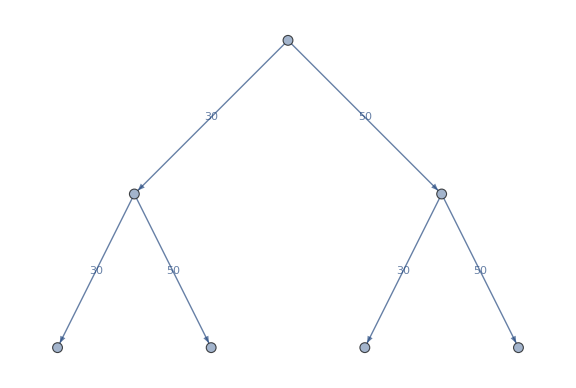

```mathematica
showGraph@evo
```